## Visualisation:

```mathematica
Manipulate[Graphics3D[Table[
{EdgeForm[],Opacity[If[RandomReal[] > p, 1,0.25]],RGBColor[0.09,0.5,0.58],Cube[{i,j,k}]},{i,size},{j,size},{k,size}],Boxed->False],
{{size,6},2,16,2},{{p, 0.5},0,1,0.1}]
```

## Function Defenitions:

```mathematica
generate3d[size_,p_] := Table[If[RandomReal[] > p, 0,1],2 ^ size,2 ^ size,2^size];
```

```mathematica
compress3d[{a_,b_},{c_,d_},{e_,f_},{g_,h_}]:=If[(a==1&&e==1)||(b==1&&f==1)||(c==1&&g==1)||(d==1&&h==1),1,0]
```

```mathematica
visualize3d[array_] := Graphics3D[Table[
{EdgeForm[],Opacity[If[array⟦i⟧⟦j⟧⟦k⟧==1,1,0.1]],RGBColor[0.09,0.5,0.58],Cuboid[{i,j,k}]},{i,1,Length[array],1},{j,1,Length[array],1},{k,1,Length[array],1}],Boxed->False]
```

```mathematica
renormOnce3d[array_] := Table[
compress3d[{array⟦i⟧⟦j⟧⟦k⟧,array⟦i⟧⟦j + 1⟧⟦k⟧},
{array⟦i+1⟧⟦j⟧⟦k⟧,array⟦i+1⟧⟦j + 1⟧⟦k⟧},
{array⟦i⟧⟦j⟧⟦k+1⟧,array⟦i⟧⟦j + 1⟧⟦k+1⟧},
{array⟦i+1⟧⟦j⟧⟦k+1⟧,array⟦i⟧⟦j + 1⟧⟦k+1⟧}],
{i,1,Length[array],2},{j,1,Length[array],2},{k,1,Length[array],2}]
```

```mathematica
renorm3d[array_] := Nest[renormOnce3d,array,Log[2,Length[array]]]
```

```mathematica
renorm3dAverage[size_,p_, number_] := Mean[
Table[renorm3d[generate3d[size,p]]⟦1⟧⟦1⟧⟦1⟧,{number}]
]
```

## Percolation function:

```mathematica
size1 = 3;(* 2^3 = 8*)
Timing[data1 = Table[renorm3dAverage[size1,p,500],{p,0,1,0.05}]]
```

```mathematica
size2 = 4;(* 2^4 = 16*)
Timing[data2 = Table[renorm3dAverage[size2,p,500],{p,0,1,0.05}]]
```

{116.679,{0,0,0,0,0,9/250,149/500,39/50,99/100,499/500,1,1,1,1,1,1,1,1,1,1,1}}

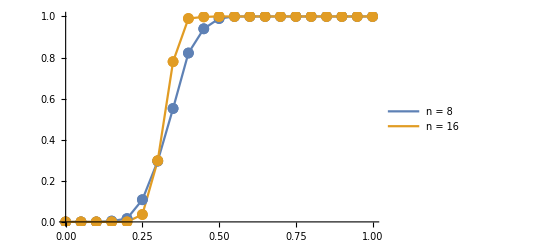

```mathematica
ListLinePlot[
{data1,data2},
Mesh->Full,DataRange->{0,1},
PlotLegends->{"n = 8","n = 16"}
]
```

```mathematica
size5 = 5; (*2^5 = 32*)
listP = {0,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.6,1};
Timing[data6 = Table[renorm3dAverage[size5,p,500],{p,listP}]]
```

{470.322,{0,0,0,1/125,11/250,13/50,347/500,117/125,1,1,1}}

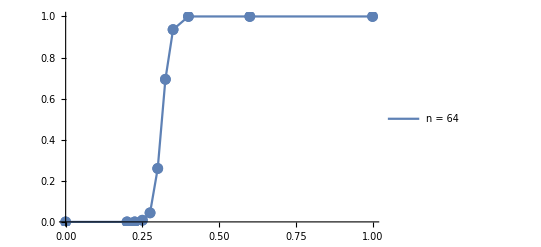

```mathematica
ListLinePlot[Partition[Riffle[listP,data6],2],Mesh->Full,DataRange->{0,1},PlotLegends->{"n = 64"}]
```

## Renormalization group visualization:

```mathematica
grid = generate3d[4,0.35];
visualize3d[grid]
```

-Graphics3D-

```mathematica
visualize3d[renormOnce3d[grid]]
```

-Graphics3D-

```mathematica
visualize3d[Nest[renormOnce3d,grid,2]]
```

-Graphics3D-

```mathematica
visualize3d[Nest[renormOnce3d,grid,3]]
```

-Graphics3D-